```mathematica
(* Mathematica*)
```

```mathematica
(* Fano Projerctive Plane as 7 Killing vectors group*)
```

```mathematica
(*incidence matrix is[1 1 1 0 0 0 0;1 0 0 1 1 0 0;1 0 0 0 0 1 1;0 1 0 1 0 1 0;0 1 0 0 1 0 1;0 0 1 1 0 0 1;0 0 1 0 1 1 0*)
```

```mathematica
s[1]={1,1 ,1 ,0,0 ,0 ,0}
s[2]={1 ,0 ,0 ,1,1, 0 ,0}
s[3]={1 ,0 ,0 ,0 ,0 ,1,1}
s[4]={0 ,1 ,0 ,1, 0, 1,0}
s[5]={0 ,1 ,0 ,0,1 ,0 ,1}
s[6]={0, 0 ,1 ,1 ,0, 0 ,1}
s[7]={0 ,0, 1,0,1 ,1,0}
```

{1,1,1,0,0,0,0}

{1,0,0,1,1,0,0}

{1,0,0,0,0,1,1}

{0,1,0,1,0,1,0}

{0,1,0,0,1,0,1}

{0,0,1,1,0,0,1}

{0,0,1,0,1,1,0}

```mathematica
ka=Table[s[i],{i,7}]
```

{{1,1,1,0,0,0,0},{1,0,0,1,1,0,0},{1,0,0,0,0,1,1},{0,1,0,1,0,1,0},{0,1,0,0,1,0,1},{0,0,1,1,0,0,1},{0,0,1,0,1,1,0}}

```mathematica
ga=GraphPlot3D[ka,ImageSize->2000];
```

```mathematica
Eigenvalues[ka]
```

{3,-√2,-√2,-√2,√2,√2,√2}

```mathematica
Table[Tr[s[i]],{i,7}]
```

{3,3,3,3,3,3,3}

```mathematica
(* Casimir Invariant*)
```

```mathematica
Sum[s[i].s[i],{i,7}]
```

21

```mathematica
(* orthogonality "zero": singularity/ punctured Polyhedron *)
```

```mathematica
Sum[s[i].Transpose[s[i]],{i,7}]
```

21

```mathematica
ka.Transpose[ka]
```

{{3,1,1,1,1,1,1},{1,3,1,1,1,1,1},{1,1,3,1,1,1,1},{1,1,1,3,1,1,1},{1,1,1,1,3,1,1},{1,1,1,1,1,3,1},{1,1,1,1,1,1,3}}

```mathematica
Transpose[ka].ka
```

{{3,1,1,1,1,1,1},{1,3,1,1,1,1,1},{1,1,3,1,1,1,1},{1,1,1,3,1,1,1},{1,1,1,1,3,1,1},{1,1,1,1,1,3,1},{1,1,1,1,1,1,3}}

```mathematica
ca=Table[2*ka[[i]].ka[[j]]/(ka[[i]].ka[[i]]),{i,7},{j,7}]
```

{{2,2/3,2/3,2/3,2/3,2/3,2/3},{2/3,2,2/3,2/3,2/3,2/3,2/3},{2/3,2/3,2,2/3,2/3,2/3,2/3},{2/3,2/3,2/3,2,2/3,2/3,2/3},{2/3,2/3,2/3,2/3,2,2/3,2/3},{2/3,2/3,2/3,2/3,2/3,2,2/3},{2/3,2/3,2/3,2/3,2/3,2/3,2}}

```mathematica
Det[ca]
```

8192/243

```mathematica
Tr[ca]
```

14

```mathematica
TableForm[ca]
```

2 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2 | 2/3 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2 | 2/3 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2 | 2/3 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2 | 2/3
2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2/3 | 2

```mathematica
Eigenvalues[ca]
```

{6,4/3,4/3,4/3,4/3,4/3,4/3}

```mathematica
p[x_]=ExpandAll[CharacteristicPolynomial[ca,x]]
```

8192/243-(114688 x)/729+(25088 x^2)/81-(8960 x^3)/27+(5600 x^4)/27-(224 x^5)/3+14 x^6-x^7

```mathematica
Discriminant[p[x],x]
```

0

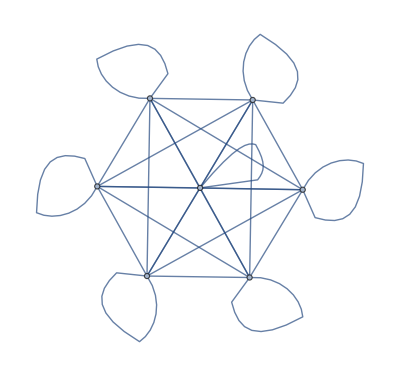

```mathematica
WeightedAdjacencyGraph[ca]
```

```mathematica
caj=Floor[Abs[ca]]
```

{{2,0,0,0,0,0,0},{0,2,0,0,0,0,0},{0,0,2,0,0,0,0},{0,0,0,2,0,0,0},{0,0,0,0,2,0,0},{0,0,0,0,0,2,0},{0,0,0,0,0,0,2}}

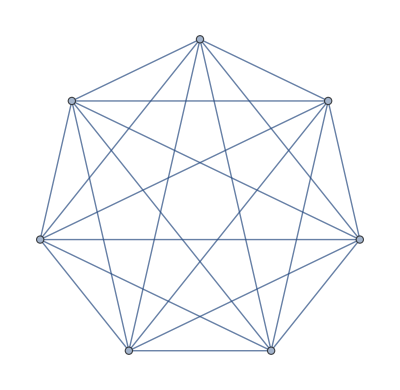

```mathematica
GraphPlot[ca]
```

```mathematica
GraphPlot3D[ca]
```

-Graphics3D-

```mathematica
(*end*)
```

```mathematica
(* incidence  matrix*)
```

```mathematica
M0=ka
```

{{1,1,1,0,0,0,0},{1,0,0,1,1,0,0},{1,0,0,0,0,1,1},{0,1,0,1,0,1,0},{0,1,0,0,1,0,1},{0,0,1,1,0,0,1},{0,0,1,0,1,1,0}}

```mathematica
MatrixForm[M0]
```

(1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1 | 0)

```mathematica
(* graph from  Adjacency Matrix*)
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
g0=FromAdjacencyMatrix[M0]
```

⁃Graph:<12,7,Undirected>⁃

```mathematica
ga=GraphPlot3D[M0,ImageSize->2000];
```

```mathematica
ShowGraph[g0];
```

```mathematica
g1=Show[GraphPlot3D[g0],ImageSize->Full];
```

```mathematica
(* make polynomial*)
```

```mathematica
CharacteristicPolynomial[M0,x]
```

-24+8 x+36 x^2-12 x^3-18 x^4+6 x^5+3 x^6-x^7

```mathematica
(* solve Polynomial*)
```

```mathematica
w=x/.NSolve[CharacteristicPolynomial[M0,x]==0,x]
```

{-1.41421,-1.41421,-1.41421,1.41421,1.41421,1.41421,3.}

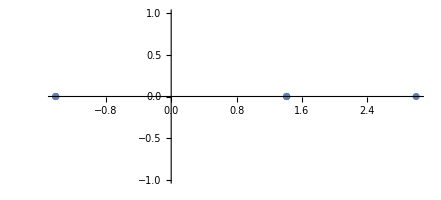

```mathematica
ComplexListPlot[w]
```

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[CharacteristicPolynomial[M0,x]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
(*For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/FanoPlane.html.*)
e={{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}
{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}
```

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

```mathematica
Table[s[i]=e[[i]],{i,7}]
```

{{1,7,5},{2,7,6},{3,7,4},{1,6,3},{3,5,2},{1,4,2},{4,5,6}}

```mathematica
w=Flatten[Table[s[i],{i,7}]]
```

{1,7,5,2,7,6,3,7,4,1,6,3,3,5,2,1,4,2,4,5,6}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[2];
```

```mathematica
Length[aa]
```

189

```mathematica
(* second chord transform*)
```

```mathematica
(*heptatonic:Black Keys{Db,Eb,F,Gb,Ab,Bb,C}*)
```

```mathematica
v={1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12,1,3,5,6,8,10,12}
```

{1,3,6,8,10,1,3,6,8,10,1,3,6,8,10,1,3,6,8,10,1,3,6,8,10,1,3,6,8,10,1,3,6,8,10}

```mathematica
Length[v]
```

35

```mathematica
PiDigits=Table[v[[aa[[i]]]],{i,Length[aa]}]
```

{1,6,6,1,10,3,1,6,6,6,10,10,1,10,3,10,1,3,1,10,3,1,3,6,3,3,8,3,8,8,8,1,1,8,10,1,3,1,3,8,1,1,1,3,6,8,1,1,10,1,3,1,3,6,1,6,6,6,10,10,6,8,10,6,10,10,1,10,3,10,1,3,6,10,10,8,10,1,10,1,3,3,1,3,3,8,8,3,6,8,3,8,8,8,1,1,8,10,1,3,8,8,6,8,10,8,10,1,1,6,6,1,10,3,1,6,6,1,6,6,6,10,10,6,8,10,1,6,6,3,6,8,6,8,10,3,1,3,3,8,8,3,6,8,3,1,3,8,1,1,1,3,6,3,1,3,3,6,8,3,3,8}

```mathematica
SeedRandom[123]
```

```mathematica
snd1=Sound[Table[SoundNote[RandomChoice[{"HighWoodblock","Snare","Sticks","SideStick","BassDrum","MidTom","LowBongo","LowTom","LowWoodblock"}],.24],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_1.mid",snd1]
```

```mathematica
snd2=Sound[Table[SoundNote[PiDigits[[i]],.24,"Piano"],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_2.mid",snd2]
```

```mathematica
snd2a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,"SynthBass2"],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_2a.mid",snd2a]
```

```mathematica
(* 8th notes*)
snd10=Sound[Table[SoundNote[PiDigits[[i]]+24,.24,"Flute"],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_10.mid",snd10]
```

```mathematica
snd3=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,RandomChoice[If[Mod[i,5]>0,{"Bass","ElectricBass","BassAndLead","PickedBass"},{"SynthBass2"}]]],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_3.mid",snd3]
```

```mathematica
w0={"Bass","ElectricBass","BassAndLead","PickedBass","SynthBass2"};
```

```mathematica
snd3a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,w0[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_3a.mid",snd3a]
```

```mathematica
w1={"AltoSax","ElectricGuitar","Piano","Banjo","Whistle"};
```

```mathematica
snd4a=Sound[Table[SoundNote[PiDigits[[i]],.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_4a.mid",snd4a]
```

```mathematica
snd4b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_4b.mid",snd4b]
```

```mathematica
snd5b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.48,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_5b.mid",snd5b]
(* quarter notes*)
```

```mathematica
snd5=Sound[Table[SoundNote[PiDigits[[i]]+24,.48,"Tinklebell"],{i,Floor[Length[PiDigits]/2]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_5.mid",snd5]
```

```mathematica
snd6=Sound[Table[SoundNote[PiDigits[[i]]-24,0.48,"SynthBass2"],{i,Floor[Length[PiDigits]/2]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_6.mid",snd6]
```

```mathematica
snd13=Sound[Table[SoundNote[PiDigits[[i]]+12,.20,"Piano"],{i,Length[PiDigits]}]]
Export["Fullerene_28symbol_substitution_BlackKeys_level2_13.mid",snd13]
```

Fullerene_28symbol_substitution_BlackKeys_level2_13.mid

```mathematica
snd14=Sound[Table[SoundNote[PiDigits[[i]]-24,.20,"SynthBass2"],{i,Length[PiDigits]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_14.mid",snd14]
```

```mathematica
wa={0.24,0.24,0.24,0.24,0.24,0.24,0.48,0.48,0.24,0.12,0.12,0.48,0.48};
```

```mathematica
Apply[Plus,wa]
```

3.84

```mathematica
snd8=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_8.mid",snd8]
```

```mathematica
wb={3*0.24,0.24,0.48,0.48,0.24,0.24,0.24,0.24,0.48,0.48};
```

```mathematica
Apply[Plus,wb]
```

3.84

```mathematica
snd4c=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_4c.mid",snd4c]
```

```mathematica
snd5c=Sound[Table[SoundNote[PiDigits[[i]]-12,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_5c.mid",snd5c]
```

```mathematica
Clear[wa,wb]
```

```mathematica
wa={0.12,0.12,0.12,0.12,0.48,0.24,0.24,0.48,0.24,0.48,0.24,0.48,0.24,0.48,0.24};
```

```mathematica
Apply[Plus,wa]
```

4.32

```mathematica
snd9=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_9.mid",snd9]
```

```mathematica
wb={0.48,0.24,0.48,0.12,0.12,0.12,0.12,0.24,0.24,0.48,0.24,0.48,0.24,0.48};
```

```mathematica
Apply[Plus,wb]
```

4.08

```mathematica
snd4d=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_4d.mid",snd4d]
snd5d=Sound[Table[SoundNote[PiDigits[[i]]-12,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["Fullerene_26symbol_substitution_BlackKeys_level2_5d.mid",snd5d]
```

```mathematica
wc={0.24,0.24,0.24,0.24,0.48,0.48,0.24,0.48,0.24,0.48,0.48,0.24,0.24,0.24,0.24,0.24,0.12,0.12,0.12,0.12,0.96};
```

```mathematica
Apply[Plus,wc]
```

6.48

```mathematica
w1={None,"Piano","Piano",None,None,"Piano","Piano",None,"Piano",None,"Piano","Piano",None,"Piano"};
```

```mathematica
snd4f=Sound[Table[SoundNote[{PiDigits[[i]]-5,PiDigits[[i]],PiDigits[[i]]+3},wc[[1+Mod[i,Length[wc]]]],w1[[1+Mod[i,8]]]],{i,Ceiling[Length[PiDigits]/3]}]]
Export["Fullerene_266symbol_substitution_BlackKeys_level2_none3_4f.mid",snd4f]
```

```mathematica
snd5f=Sound[Table[SoundNote[{PiDigits[[i]]-5-24,PiDigits[[i]]-24,PiDigits[[i]]+3-24},wc[[1+Mod[i,Length[wc]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]/4]}]]
Export["SFullerene_26symbol_substitution_BlackKeys_level2_5f.mid",snd5f]
```